```mathematica
NS["study_maxent_sample_limitations","C:\\Users\\pglpm\\repositories\\neurobayes\\functional_connectivity"]
```

```mathematica
lh[s1_,s2_,j12_,h1_,h2_]=Block[
{list=Exp[s1*j12*s2+h1*s1+h2*s2]},list/Sum[list,{s1,0,1},{s2,0,1},{s3,0,1}]]
```

ⅇ^(h1 s1+h2 s2+j12 s1 s2)/(2+2 ⅇ^h1+2 ⅇ^h2+2 ⅇ^(h1+h2+j12))

```mathematica
nd[j_]=PDF[NormalDistribution[0,1],j]
```

(ⅇ^(-j^2/2))/(√(2 π))

```mathematica
{t1,t2}=RandomInteger[{0,1},2]
```

{0,1}

```mathematica
upostjh2[j12_,h1_,h2_]=FS[lh[t1,t2,j12,h1,h2]*nd[j12]*nd[h1]*nd[h2]]
```

(ⅇ^(1/2 (-h1^2-(-2+h2) h2-j12^2)))/(4 √2 (1+ⅇ^h1+ⅇ^h2+ⅇ^(h1+h2+j12)) π^(3/2))

```mathematica
normjh1=NIntegrate[upostjh2[j12,h1,h2],{j12,-Infinity,+Infinity},{h1,-Infinity,+Infinity},{h2,-Infinity,+Infinity},PrecisionGoal->2,AccuracyGoal->+Infinity]
```

0.120846

```mathematica
margj12a[j12_]:=NIntegrate[upostjh2[j12,h1,h2],{h1,-Infinity,+Infinity},{h2,-Infinity,+Infinity},PrecisionGoal->2,AccuracyGoal->+Infinity]/normjh1
```

```mathematica
margh1a[h1_]:=NIntegrate[upostjh2[j12,h1,h2],{j12,-Infinity,+Infinity},{h2,-Infinity,+Infinity},PrecisionGoal->2,AccuracyGoal->+Infinity]/normjh1
```

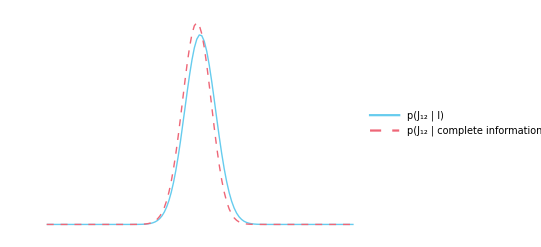

```mathematica
Plot[{nd[j12],margj12a[j12]},{j12,-10,10},PlotPoints->3,MaxRecursion->Auto,PlotRange->{All,All},
FrameLabel->{Subscript[J,12] ,"prob. density"},PlotLegends->Placed[{HoldForm["p"[Subscript[J,12] "| I"]],HoldForm["p"[Subscript[J,12] "| complete information, I"]]},{Left,Top}],ImageSize->a4shortside]
```

```mathematica
Export["prior_post_j12.png",Style[%,Magnification->1],ImageResolution->300]
```

prior_post_j12.png

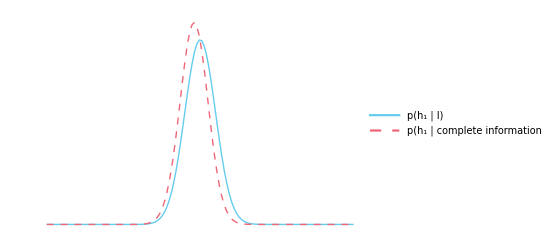

```mathematica
Plot[{nd[j12],margh1a[j12]},{j12,-10,10},PlotPoints->3,MaxRecursion->Auto,PlotRange->{All,All},
FrameLabel->{Subscript[h,1] ,"prob. density"},PlotLegends->Placed[{HoldForm["p"[Subscript[h,1] "| I"]],HoldForm["p"[Subscript[h,1] "| complete information, I"]]},{Left,Top}],ImageSize->a4shortside]
```

```mathematica
Export["prior_post_h1.png",Style[%,Magnification->1],ImageResolution->300]
```

prior_post_h1.png

```mathematica
(* Three neurons *)
```

```mathematica
lh[s1_,s2_,s3_,j12_,j13_,j23_,h1_,h2_,h3_]=Block[
{list=Exp[s1*j12*s2+s1*j13*s3+s2*j23*s3+h1*s1+h2*s2+h3*s3]},list/Sum[list,{s1,0,1},{s2,0,1},{s3,0,1}]]
```

ⅇ^(h1 s1+h2 s2+j12 s1 s2+h3 s3+j13 s1 s3+j23 s2 s3)/(1+ⅇ^h1+ⅇ^h2+ⅇ^h3+ⅇ^(h1+h2+j12)+ⅇ^(h1+h3+j13)+ⅇ^(h2+h3+j23)+ⅇ^(h1+h2+h3+j12+j13+j23))

```mathematica
nd[j_]=PDF[NormalDistribution[0,1],j]
```

(ⅇ^(-j^2/2))/(√(2 π))

```mathematica
{t1,t2,t3}=RandomInteger[{0,1},3]
```

{0,1,0}

```mathematica
upostjh2[j12_,j13_,j23_,h1_,h2_,h3_]=FS[lh[t1,t2,t3,j12,j13,j23,h1,h2,h3]*nd[j12]*nd[j13]*nd[j23]*nd[h1]*nd[h2]*nd[h3]]
```

(ⅇ^(1/2 (-h1^2-(-2+h2) h2-h3^2-j12^2-j13^2-j23^2)))/(8 (1+ⅇ^h1+ⅇ^h2+ⅇ^h3+ⅇ^(h1+h2+j12)+ⅇ^(h1+h3+j13)+ⅇ^(h2+h3+j23)+ⅇ^(h1+h2+h3+j12+j13+j23)) π^3)

```mathematica
normjh=NIntegrate[upostjh2[j12,j13,j23,h1,h2,h3],{j12,-Infinity,+Infinity},{j13,-Infinity,+Infinity},{j23,-Infinity,+Infinity},{h1,-Infinity,+Infinity},{h2,-Infinity,+Infinity},{h3,-Infinity,+Infinity},PrecisionGoal->2,AccuracyGoal->+Infinity]
```

0.112763

```mathematica
margj12[j12_]:=NIntegrate[upostjh2[j12,j13,j23,h1,h2,h3],{j13,-Infinity,+Infinity},{j23,-Infinity,+Infinity},{h1,-Infinity,+Infinity},{h2,-Infinity,+Infinity},{h3,-Infinity,+Infinity},PrecisionGoal->2,AccuracyGoal->+Infinity]/normjh
```

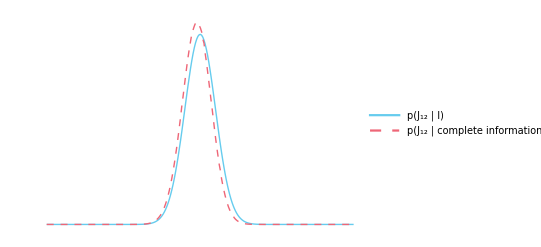

```mathematica
Plot[{nd[j12],margj12[j12]},{j12,-10,10},PlotPoints->5,PlotRange->{All,All},
FrameLabel->{Subscript[J,12] ,"prob. density"},PlotLegends->Placed[{HoldForm["p"[Subscript[J,12] "| I"]],HoldForm["p"[Subscript[J,12] "| complete information, I"]]},{Left,Top}],ImageSize->a4shortside]
```

```mathematica
expng["prior_post_j12_N3",%]
```

prior_post_j12_N3.png